```mathematica
solve[r1i_,r2i_,k_,end_]:=NDSolve[{
r1'[t]==-k*r1[t]*r2[t],
r2'[t]==-k*r1[t]*r2[t],
p1'[t]==k*r1[t]*r2[t],
p2'[t]==k*r1[t]*r2[t],
p1[0]==0,
p2[0]==0,
r1[0]==r1i,
r2[0]==r2i
},{r1,r2,p1,p2},{t,0,end}]
```

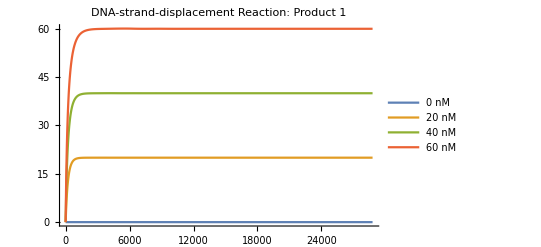

```mathematica
time=8*60*60;
s1=solve[100*10^-9,0*10^-9,5*10^4,time];
s2=solve[100*10^-9,20*10^-9,5*10^4,time];
s3=solve[100*10^-9,40*10^-9,5*10^4,time];
s4=solve[100*10^-9,60*10^-9,5*10^4,time];
Plot[{Evaluate[p1[t]/.s1]/10^-9,Evaluate[p1[t]/.s2]/10^-9,Evaluate[p1[t]/.s3]/10^-9,Evaluate[p1[t]/.s4]/10^-9},{t,0,time},PlotRange->All,PlotLegends->{"0 nM","20 nM","40 nM","60 nM"},PlotLabel->"DNA-strand-displacement Reaction: Product 1"]
```

```mathematica
1x TE: 10 mM Tris , 1 mM EDTA
100x TE: 1 M Tris, 0.1 M EDTA
1xTE/10×Mg2+: 125 mM Mg2+
100x TE, 1 M MgCl2, H2O
 5 mL of 1×TE/10×Mg2+: 50μL 100x TE,  625μL 1 M MgCl2, 4.325 mL H2O
```

```mathematica
TETris1x=10*10^-3;
TEEDTA1x=1*10^-3;
TETris100x=TETris1x*100
TEEDTA100x=TEEDTA1x*100
```

1

1/10

```mathematica
TE1xMg10xMg=125*10^-3;
MG=1;
TE5mlTEMg=5*10^-3/TETris100x*TETris1x
Mg5mlTEMg=5*10^-3/MG*TE1xMg10xMg
H2O=5*10^-3-TE5mlTEMg-Mg5mlTEMg
```

1/20000

1/1600

173/40000

Rep6-t (top) can be in excess
 Rep6-t, Rep6-b: 100 µM in 1xTE 
 100 µL of 10 µM Rep6
 Rep6-t: 12  µL
 Rep6-b: 10  µL
 1×TE/10×Mg2+: 10  µL
 1×TE: 68  µL

```mathematica
w5,6: 100 µM
5 nM w5,6 in 500 µL
w5,6: 0.025 µL
min pipetting volume: 1 µL
0.025 µL is less than 1 µL
200 µL of 2.5 µM w5,6
w5,6: 5 µL
TE: 195 µL

20 nM Rep6 and 0/5/10/15 nM w5,6 in a 500 µL solution
1×TE: 
1×TE/10×Mg2+: 
1000 µM 20T: 
10 µM Rep6: 
2.5 µM w5,6: 0/5/10/15 * 500 = 2.5 * 0/0.025/
20 µM something
```